{Leaver1,Leaver2,Leaver3,Grim,WSLS,TFT,CCDCC}

xv = {0.,0.,0.,0.25,0.25,0.25,0.25}

Lij = (7.13012 | 7.13012 | 7.13012 | 3.42306 | 10.9619 | 3.42306 | 10.9619
7.13012 | 7.13012 | 7.13012 | 1.37968 | 1.64349 | 1.37968 | 1.64349
7.13012 | 7.13012 | 7.13012 | 2.60477 | 3.14755 | 2.60477 | 3.14755
3.42306 | 1.37968 | 2.60477 | 20. | 20. | 20. | 20.
10.9619 | 1.64349 | 3.14755 | 20. | 20. | 20. | 20.
3.42306 | 1.37968 | 2.60477 | 20. | 20. | 20. | 20.
10.9619 | 1.64349 | 3.14755 | 20. | 20. | 20. | 20.)

Distribution in the pool corresponding to xv : {0,0,0,0.25,0.25,0.25,0.25}

Fij = (2.64755 | 2.64755 | 2.64755 | 1.97803 | 2.7675 | 1.97803 | 2.7675
2.64755 | 2.64755 | 2.64755 | 3.45823 | 3.44761 | 3.45823 | 3.44761
2.64755 | 2.64755 | 2.64755 | 2.23101 | 2.4009 | 2.23101 | 2.4009
1.85487 | 0.974395 | 2.20161 | 1.75017 | 2.60865 | 1.88998 | 2.66042
2.43909 | 1.25716 | 2.30387 | 1.65204 | 2.73755 | 2.26288 | 2.79445
1.85487 | 0.974395 | 2.20161 | 1.73419 | 2.24529 | 2.31034 | 2.47876
2.43909 | 1.25716 | 2.30387 | 1.64612 | 2.63866 | 2.43322 | 2.54761)

Payoff of each strategy at xv: {2.57964,3.45246,2.32397,2.2273,2.36173,2.19215,2.3164}

Expected change of each strategy at xv = {0.00714286,0.00714286,0.00714286,-0.0102747,0.00376256,-0.0139459,-0.000970566}

We solve the differential equation numerically (with NDSolve), starting at the initial point: {0,0,0,1/4,1/4,1/4,1/4}

InterpolatingFunction[…]

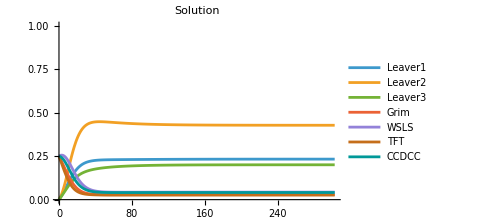

{{0,0,0,1/4,1/4,1/4,1/4},InterpolatingFunction[…],302.143,{0.232947,0.42761,0.20036,0.0280488,0.0432249,0.0267794,0.0410298}}

```mathematica
(* PARAMETERS *)

(* continuation probability for partnerships*)
δ=Rationalize[0.95,0];
(* action error rate *)
ϵ=Rationalize[0.05,0];
(* probability of experimentation *)
μ=Rationalize[0.05,0];

payoffs={3,0,4,1}; (* {R,S,T,P} *)

(* set of strategies you want to include*)
strategies={
leaver1,
leaver2,
leaver3,
grim,
WSLS,
TFT,
{c,c,d,c,c}
};

(*initial point, whole population*)
xv=Rationalize[{0,0,0,0.25,0.25,0.25,0.25},0];

(* parameteres for the solution trajectory*)
tMax=1000;
tolerance=10.^-6;

(*END PARAMETERS *)

If[Total[xv]!=1.,Print[Style["Total[xv] != 1",18,Red]]];
Map[StrategyName,strategies]
Print["xv = ",N@xv];

LMatrix=Outer[ExpectedTimeUntilBreakUp[#1,#2,ϵ,δ]&,strategies,strategies,1];
Print["Lij = ",N@MatrixForm@LMatrix];
Print["Distribution in the pool corresponding to xv : ",N[PoolFromPop[xv,strategies,ϵ,δ],6]];

FMatrix=Outer[F[#1,#2,ϵ,δ,payoffs]&,strategies,strategies,1];
Print["Fij = ",N[MatrixForm@FMatrix,6]];
Print["Payoff of each strategy at xv: ",N[Fx[xv,strategies,ϵ,δ,payoffs],6]] 

Print["Expected change of each strategy at xv = ",N[ExpectedChange[xv,strategies,ϵ,δ,μ,payoffs],6]]; 

sol=NDSolveMeanDynamics[strategies,ϵ,δ,μ,xv,payoffs,1,tMax,tolerance,6]
finalpoint=Last[sol];
```

# Source code

## Strategies

```mathematica
c=0;d=1;l=2;

c0a={c,c,l,l,c};
c0b={c,c,l,l,l};
leaver1={d,c,l,d,c};
leaver2 = {d,c,l,l,c};
leaver3={d,c,l,c,c};
c1b = {d,c,l,l,c};
defector={d,d,d,d,d};
cooperator={c,c,c,c,c};
defectAndLeave = {d,l,l,l,l};
WSLS = {c,c,d,d,c};
bWSLS = {d,c,d,d,c};
grim = {c,c,d,d,d};
grim2 = {c,c,d,d,c};
TFT = {c,c,d,c,d};
TFTlike = {c,c,d,c,c};
DDLDC = {d,d,l,d,c};

StrategyName[s_List]:=Switch[s,
{0,0,2,2,0},"c0a",
{0,0,2,2,2},"c0b",
{1,0,2,1,0},"Leaver1",
{1,0,2,2,0},"Leaver2",
{1,0,2,0,0},"Leaver3",
{1,1,1,1,1},"defector",
{0,0,0,0,0},"cooperator",
{1,2,2,2,2},"defectAndLeave",
{0,0,1,1,0},"WSLS",
{1,0,1,1,0},"bWSLS",
{0,0,1,1,1},"Grim",
{0,0,1,0,1},"TFT",
{0,0,1,0,0},"CCDCC",
{1,1,2,1,0},"DDLDC",
_,ToLetters[s]
];
ToLetters[s_List]:=StringJoin[s/.{0->"C",1->"D",2->"L"}];
```

## F_i(e_j) and L_ij

```mathematica
(* CORE FUNCTIONS, 
to compute F[i,ej] = Subscript[F, i](Subscript[e, j]) = Payoff of i on monomorphic population state Subscript[e, j]  
and to compute the expected time until breakup, i.e. Lij *)

(* actions can be 0 = cooperate, 1 = defect, or 2 = leave *)
Outcome[a1_,a2_]:=If[a1!=2&&a2!=2,1+2*a1+a2,0];
(*cc=1; cd=2; dc=3; dd=4; xl or lx = 0*)
(*outcome 0 means that the couple has broken up*)

(* the outcome from the other player's perspective *)
ReverseOutcome[o_]:=Switch[o,
Outcome[0,1],Outcome[1,0],
Outcome[1,0],Outcome[0,1],
_,o];

(* The two actions in an outcome at the game are 0 (cooperate) or 1 (defect) *)
Action1[o_]:=If[o==Outcome[0,0]||o==Outcome[0,1],0,1];
Action2[o_]:=If[o==Outcome[0,0]||o==Outcome[1,0],0,1];

(* Action after outcome. The outcome is seen from the perspective of the individual *)
(*cc=1; cd=2; dc=3; dd=4; xl or lx = 0*)
ActionAfter[s_List,outcome_]:=s[[1+outcome]];

(* 
Match returns the Tij and the sequence of outcomes in a match s1 vs s2: 
A. If ϵ==0
a. If they never break: {∞,{initial sequence of outcomes, cyclic sequence of outcomes}}
 b. If they break after t outcomes: {t,sequence of outcomes}

B.If ϵ!=0, the sequence is a distribution of outcomes at each timestep. This function returns a matrix, where row i is the distribution over outcomes at timestep i. 
*)
Match[s1_,s2_,ϵ_:0,δ_:1,timesteps_:10]:=Module[{a1=First[s1],a2=First[s2],t=0,sequence,pos,M,initial},
If[ϵ===0&&δ===1,
sequence={Outcome[a1,a2]};
While[Outcome[a1,a2]!=0&&t<1000,
{a1,a2}={ActionAfter[s1,Outcome[a1,a2]],ActionAfter[s2,Outcome[a2,a1]]};
If[MemberQ[sequence,Outcome[a1,a2]],
(* This outcome has already been observed before *)
t=∞
,
t = t+1;
];
AppendTo[sequence,Outcome[a1,a2]];
];
If[t==∞,
pos=First@FirstPosition[sequence,Outcome[a1,a2]];
{t,{sequence[[;;pos-1]],sequence[[pos;;-2]]}(*/.{0->"C",1->"D"}*)},
{t,sequence[[;;-2]](*/.{0->"C",1->"D",2->"L"}*)}
]
,
(* ϵ!=0 or δ!=1 *)
M=TransitionMatrix[s1,s2,ϵ,δ];
initial=FirstOutcomeDistribution[s1,s2,ϵ];
Prepend[Table[initial.MatrixPower[M,i],{i,1,timesteps}],initial]
]
];

FirstOutcomeDistribution[s1_,s2_,ϵ_:0]:=
Flatten@Outer[Times,(1-ϵ)UnitVector[1+First[s1]]+ϵ({1,1}-UnitVector[1+First[s1]]),(1-ϵ)UnitVector[1+First[s2]]+ϵ({1,1}-UnitVector[1+First[s2]])];

Payoff[o_,payoffs_:{3,0,4,1}]:=Module[{R,S,T,P},
{R,S,T,P}=payoffs;
Switch[o,
(*cc=1; cd=2; dc=3; dd=4; xl or lx = 0*)
1,R,
2,S,
3,T,
4,P,
_,"no"
]];

(* F[i,ej] = Subscript[F, i](Subscript[e, j]) = Payoff of i on monomorphic population state Subscript[e, j] *)
F[i_,ej_,ϵ_:0,δ_:1,payoffs_:{3,0,4,1}]:=Module[{Tij,sequence,initialPhase,cycle,R,S,T,P},
{R,S,T,P}=payoffs;
If[ϵ===0&&δ===1,
{Tij,sequence}=Match[i,ej];
If[Tij<∞,
1/Tij∑_(t=1)^Tij Payoff[sequence[[t]],payoffs]
,
(*Tij == ∞*)
{initialPhase,cycle}=sequence;
1/Length[cycle]∑_(t=1)^Length[cycle] Payoff[cycle[[t]],payoffs]
]
,
(* ϵ!=0 or δ!=1 *)
(* limitingPayoff *)
{R,S,T,P}.AsymptoticDistribution[i,ej,ϵ,δ]
]
];

(* ProbsOfThe3Actions returns a vector with the probability of C, D and L, for strategy s after outcome o in the presence of error ϵ. The outcome is seen from the perspective of the agent*)
ProbsOfThe3Actions[s_List,outcome_,ϵ_]:=Module[{actionNoNoise=ActionAfter[s,outcome]},
Switch[actionNoNoise,
0(*Cooperate*), {1-ϵ,ϵ,0},
1(*Defect*), {ϵ,1-ϵ,0},
2(*Leave*),{0,0,1}
]
];

ProbOfLeaving[s_List,outcome_,ϵ_]:=Last[ProbsOfThe3Actions[s,outcome,ϵ]];

(* ProbOfPartnershipBreakup returns the probability that the partnership breaks after the given outcome. *)
ProbOfPartnershipBreakup[s1_List,s2_List,outcome_,ϵ_,δ_]:=Module[{p1=ProbOfLeaving[s1,outcome,ϵ],p2=ProbOfLeaving[s2,ReverseOutcome@outcome,ϵ],pEnd},
pEnd=p1+p2-p1*p2; (* = 1-(1-p1)(1-p2) = Probability of endogenous break-up *)
1-(1-pEnd)δ 
];

(* TransitionProb returns the probability that, in a contest between s1 and s2, the partnership goes from outcome o1 to outcome o2 in the presence of error ϵ. In this Markov chain, outcome 0 is a state*)
TransitionProb[s1_List,s2_List,o1_,o2_,ϵ_,δ_]:=Module[{probBreakup=ProbOfPartnershipBreakup[s1,s2,o1,ϵ,δ]},
If[o2==0,(*outcome 0 means that the couple has broken up*)
If[o1==0,0,probBreakup]
,
If[o1==0,1,δ]*((ProbsOfThe3Actions[s1,o1,ϵ])[[1+Action1[o2]]])*((ProbsOfThe3Actions[s2,ReverseOutcome[o1],ϵ])[[1+Action2[o2]]])
]
];

TransitionMatrixIncludingBreakUp[s1_List,s2_List,ϵ_,δ_]:=Module[{allOutcomes=Range[0,4]},
Outer[TransitionProb[s1,s2,#1,#2,ϵ,δ]&,allOutcomes,allOutcomes]
];

TransitionMatrix[s1_List,s2_List,ϵ_,δ_]:=Module[{M,outflow,inflow},
M=TransitionMatrixIncludingBreakUp[s1,s2,ϵ,δ];
outflow=Rest@First[M];
inflow=First[Mᵀ];
Map[(Rest[M[[#]]]+inflow[[#]]*outflow)&,Range[2,5]]
];

AsymptoticDistribution[s1_List,s2_List,ϵ_,δ_]:=FullSimplify[Normalize[Abs@First@Eigenvectors[TransitionMatrix[s1,s2,ϵ,δ]ᵀ,1],Total], Assumptions->{0<=ϵ<=1,0<=δ<=1}];

(* Lij
Theorem 11.5, p. 419, https://chance.dartmouth.edu/teaching_aids/books_articles/probability_book/book.html *)
ExpectedTimeUntilBreakUp[s1_List,s2_List,ϵ_,δ_]:=Module[{P=TransitionMatrixIncludingBreakUp[s1,s2,ϵ,δ],initialDistribution=FirstOutcomeDistribution[s1,s2,ϵ]},
initialDistribution.(Inverse[IdentityMatrix[4]-P[[2;;,2;;]]].Table[1,{4}])
];
```

## Pool composition p from population distribution x

```mathematica
(* CORE FUNCTIONS, to compute the composition of the pool of singles p from the composition in the population x *)

PoolFromPop[x_?(VectorQ[#,NumericQ]&),strategies_List,ϵ_,δ_]:=Module[{L},
L=Outer[ExpectedTimeUntilBreakUp[#1,#2,ϵ,δ]&,strategies,strategies,1];
PoolFromPop[x,strategies,ϵ,δ,L]
];

PoolFromPop[x_?(VectorQ[#,NumericQ]&),strategies_List,ϵ_,δ_,L_]:=Module[{n=Length[strategies],p,pvars,sol},
If[Length[x]!=n,Print[Style["The dimension of the population distribution provided does not match the number of strategies",18,Red]];Quit[]];
If[Or[Count[x,1]>0,Count[x,1.]>0],Return[x]];

pvars=Table[p[i],{i,n}];
sol=SolveValues[Join[
{Normalize[Rationalize[x,0],Total]==pvars*L.pvars},
Table[0≤p[i]≤1,{i,n}]
],pvars,Reals];
Normalize[First@sol,Total]
];
```

## Strategies payoffs in a population x, i.e. Fx

```mathematica
Fx[x_?(And[VectorQ[#,NumericQ],VectorQ[#,NonNegative]]&),strategies_List,ϵ_,δ_,payoffs_:{3,0,4,1}]:=Module[{FMatrix,LMatrix},
FMatrix=Outer[F[#1,#2,ϵ,δ,payoffs]&,strategies,strategies,1];
LMatrix=Outer[ExpectedTimeUntilBreakUp[#1,#2,ϵ,δ]&,strategies,strategies,1];
Fx[x,strategies,ϵ,δ,LMatrix,FMatrix]
]

Fx[x_?(And[VectorQ[#,NumericQ],VectorQ[#,NonNegative]]&),strategies_List,ϵ_,δ_,LMatrix_List,FMatrix_List]:=Module[{p},
p=PoolFromPop[x,strategies,ϵ,δ,LMatrix];
Total[FMatrixᵀ*(p*LMatrixᵀ)]/Total[p*LMatrixᵀ]
]
```

## Dynamics

```mathematica
(* DYNAMICS *)

ExpectedChange[x_?(And[VectorQ[#,NumericQ],VectorQ[#,NonNegative]]&),strategies_List,ϵ_,δ_,μ_,payoffs_:{3,0,4,1}]:=Module[{LMatrix,FMatrix},
FMatrix=Outer[F[#1,#2,ϵ,δ,payoffs]&,strategies,strategies,1];
LMatrix=Outer[ExpectedTimeUntilBreakUp[#1,#2,ϵ,δ]&,strategies,strategies,1];
ExpectedChange[x,strategies,ϵ,δ,μ,LMatrix,FMatrix]
];

ExpectedChange[x_?(And[VectorQ[#,NumericQ],VectorQ[#,NonNegative]]&),strategies_List,ϵ_,δ_,μ_,LMatrix_,FMatrix_]:=Module[{Π,n=Length[strategies]},
Π=Fx[x,strategies,ϵ,δ,LMatrix,FMatrix];
(1-μ)*ReplicatorMS[x,Π]+μ*(ConstantArray[1/n,n]-x)
(*EC=(1-m)*ReplicatorMS[x,Π]+m*(ConstantArray[1/n,n]-x);
Normalize[1/n+EC,Total]-1/n*)
];

(* DYNAMICS *)
ReplicatorMS[x_,Π_]:=Module[{avgPayoff=x.Π},
Piecewise[{{1/avgPayoff,avgPayoff>0}},0]*((x*Π)-avgPayoff*x)
];

(*Replicator[x_,Π_]:=(x*Π)-(x.Π) x;*)
```

## Numerically solve mean dynamics

```mathematica
NDSolveMeanDynamics[strategies_List,ϵ_,δ_,μ_,ip_:{},payoffs_:{3,0,4,1},verbosity_:1,maxTime_:300,tolerance_:10.^-4,accuracyGoal_:6]:=Module[{x,t,n=Length[strategies],LMatrix,FMatrix,projectedEM,sol,finalTime,initialPoint,i,strategyNames},

If[ip=={},initialPoint=First[RandomPoints[n,1]],initialPoint=ip];

FMatrix=Outer[F[#1,#2,ϵ,δ,payoffs]&,strategies,strategies,1];
LMatrix=Outer[ExpectedTimeUntilBreakUp[#1,#2,ϵ,δ]&,strategies,strategies,1];

projectedEM[v_]:=(IdentityMatrix[n]-1/n ConstantArray[1,{n,n}]).(ExpectedChange[v,strategies,ϵ,δ,μ,LMatrix,FMatrix]);

(*NDSolve*)

If[verbosity≥1,
Print["We solve the differential equation numerically (with NDSolve), starting at the initial point: ", initialPoint];
];

finalTime=maxTime;

sol=NDSolveValue[
{x'[t]==projectedEM[x[t]],x[0]==initialPoint,WhenEvent[Evaluate[Norm[x'[t]]<tolerance], {finalTime=t,"StopIntegration"}]},
x,{t,0,maxTime},AccuracyGoal->accuracyGoal,Method->{"EquationSimplification"->"Residual"}];

Print[sol];

If[verbosity≥1,
strategyNames=Map[StrategyName,strategies];
Print@
Plot[Evaluate@Table[Tooltip[Indexed[sol[t],k],strategyNames[[k]]],{k,n}],{t,0,finalTime},PlotLegends->Map[StrategyName,strategies],PlotLabel->"Solution",ImageSize->Medium,PlotRange->{0,1}];
];
(*Plot[Evaluate@MapThread[Tooltip,{Map[#[t]&,sol],Map[StrategyName,strategies]}],{t,0,finalTime},]*)

{initialPoint,sol,finalTime,sol[finalTime]}

]

RandomPoints::usage="RandomPoints[n, nPoints] returns a list of nPoints random points for a game with n strategies" ;
RandomPoints[n_,nPoints_]:=Module[{},Map[#/Total[#]&,Table[RandomReal[1,n],nPoints]]
];

SimplexMesh::usage="SimplexMesh[nStrategies, nAgents] returns a list of all the possible strategy distributions in a population of nAgents agents who can choose one of nStrategies possible strategies. The number of possible distributions is Binomial[nAgents+nStrategies-1, nAgents]" ;
SimplexMesh[nStrategies_,nAgents_]:=Flatten[Permutations/@IntegerPartitions[nAgents,{nStrategies},Range[0,nAgents]],1]/N@nAgents;
```